```mathematica
(*(ccdata[7]/.{x_,y_}/;x>maxyx->{x,0})[[All,2]]*)
```

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Define BWs

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;
```

## Charmonium

### Import Data

```mathematica
Tscanc=Round[1000 Join[Table[i,{i,0.15,0.16,0.001}],{0.162},Table[i,{i,0.164,0.170,0.003}],Table[i,{i,0.1740,0.2220,0.003}],Table[i,{i,0.224,0.230,0.003}],Table[i,{i,0.234,0.249,0.003}],Table[i,{i,0.253,0.3,0.003}]]]
```

{150,151,152,153,154,155,156,157,158,159,160,162,164,167,170,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,224,227,230,234,237,240,243,246,249,253,256,259,262,265,268,271,274,277,280,283,286,289,292,295,298}

```mathematica
Do[ccdata[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"spectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdata[n],Joined->True],{n,1,Length[Tscanc],1}]
```

```mathematica
Do[ccdatau[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"uspectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatau[n],Joined->True],{n,1,Length[Tscanc],1}]
```

```mathematica
Do[ccdatal[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"lspectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatal[n],Joined->True],{n,1,Length[Tscanc],1}]
```

### Fitting

```mathematica
fit[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];
maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
If[maxxs[[2]]/maxxs[[1]]≤1.001,maxxs=Delete[maxxs,2]];
maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
bad={};
Do[If[maxys[[i]]<maxys[[i+1]],bad=Append[bad,i]],{i,Length[maxys]-1}]
Do[maxxs=Delete[maxxs,bad[[i]]];maxys=Delete[maxys,bad[[i]]];maxxis=Delete[maxxis,bad[[i]]];,{i,Length[bad]}]
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];
mins=Append[Prepend[mins,maxxis[[1]]-2 (mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),maxyi+3(maxyi-hwhmi)};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
Do[If[Or[2 input[n][[hwhmi[[-i]],2]]≤0.5 maxys[[-i]],2 input[n][[hwhmi[[-i]],2]]≥1.5 maxys[[-i]]],hwhmi[[-i]]=maxxis[[-i]]],{i,Length[hwhmi]-1}];
bad=Position[maxxis-hwhmi,0];
hwhmi=DeleteCases[maxxis-hwhmi,0];
maxxis=Delete[maxxis,bad];
maxxs=Delete[maxxs,bad];
maxys=Delete[maxys,bad];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];
mins=Append[Prepend[mins,maxxis[[1]]-2 (mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),maxyi+3(maxyi-hwhmi)};
hwhmi={hwhmi};];
If[mins[[1]]≤0,mins[[1]]=1];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
hwhmi=DeleteCases[maxxis-hwhmi,0];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[maxxis[[i]]-hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[mins[[i]];;mins[[i+1]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;]
```

```mathematica
fit[ccdata,ccmodel,Tscanc]
fit[ccdatau,ccmodelu,Tscanc];
fit[ccdatal,ccmodell,Tscanc];
```

### Store Results

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];
If[Length[ccmodel[[i]]]>1,ccTcut=i];If[Length[ccmodelu[[i]]]>1,ccuTcut=i];If[Length[ccmodell[[i]]]>1,cclTcut=i];,{i,Length[ccmodel]}];
```

```mathematica
wrfitcc=Range[Length[ccmodel]];
Do[wrfitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[wrfitcc[[i,ii]]=wr/.ccmodel[[i,ii]]["BestFitParameters"],{ii,Length[wrfitcc[[i]]]}],{i,Length[wrfitcc]}]

wrfitccu=Range[Length[ccmodelu]];
Do[wrfitccu[[i]]=Range[Length[ccmodelu[[i]]]],{i,Length[ccmodelu]}];
Do[Do[wrfitccu[[i,ii]]=wr/.ccmodelu[[i,ii]]["BestFitParameters"],{ii,Length[wrfitccu[[i]]]}],{i,Length[wrfitccu]}]

wrfitccl=Range[Length[ccmodell]];
Do[wrfitccl[[i]]=Range[Length[ccmodell[[i]]]],{i,Length[ccmodell]}];
Do[Do[wrfitccl[[i,ii]]=wr/.ccmodell[[i,ii]]["BestFitParameters"],{ii,Length[wrfitccl[[i]]]}],{i,Length[wrfitccl]}]

Γfitcc=Range[Length[ccmodel]];
Do[Γfitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[Γfitcc[[i,ii]]=Γ/.ccmodel[[i,ii]]["BestFitParameters"],{ii,Length[Γfitcc[[i]]]}],{i,Length[Γfitcc]}]

Γfitccu=Range[Length[ccmodelu]];
Do[Γfitccu[[i]]=Range[Length[ccmodelu[[i]]]],{i,Length[ccmodelu]}];
Do[Do[Γfitccu[[i,ii]]=Γ/.ccmodelu[[i,ii]]["BestFitParameters"],{ii,Length[Γfitccu[[i]]]}],{i,Length[Γfitccu]}]

Γfitccl=Range[Length[ccmodell]];
Do[Γfitccl[[i]]=Range[Length[ccmodell[[i]]]],{i,Length[ccmodell]}];
Do[Do[Γfitccl[[i,ii]]=Γ/.ccmodell[[i,ii]]["BestFitParameters"],{ii,Length[Γfitccl[[i]]]}],{i,Length[Γfitccl]}]

constfitcc=Range[Length[ccmodel]];
Do[constfitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[constfitcc[[i,ii]]=const/.ccmodel[[i,ii]]["BestFitParameters"],{ii,Length[constfitcc[[i]]]}],{i,Length[constfitcc]}]

constfitccu=Range[Length[ccmodelu]];
Do[constfitccu[[i]]=Range[Length[ccmodelu[[i]]]],{i,Length[ccmodelu]}];
Do[Do[constfitccu[[i,ii]]=const/.ccmodelu[[i,ii]]["BestFitParameters"],{ii,Length[constfitccu[[i]]]}],{i,Length[constfitccu]}]

constfitccl=Range[Length[ccmodell]];
Do[constfitccl[[i]]=Range[Length[ccmodell[[i]]]],{i,Length[ccmodell]}];
Do[Do[constfitccl[[i,ii]]=const/.ccmodell[[i,ii]]["BestFitParameters"],{ii,Length[constfitccl[[i]]]}],{i,Length[constfitccl]}]

areafitcc=Range[Length[ccmodel]];
Do[areafitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[areafitcc[[i,ii]]=π/2 constfitcc[[i,ii]] Γfitcc[[i,ii]],{ii,Length[areafitcc[[i]]]}],{i,Length[areafitcc]}]

areafitccu=Range[Length[ccmodelu]];
Do[areafitccu[[i]]=Range[Length[ccmodelu[[i]]]],{i,Length[ccmodelu]}];
Do[Do[areafitccu[[i,ii]]=π/2 constfitccu[[i,ii]] Γfitccu[[i,ii]],{ii,Length[areafitccu[[i]]]}],{i,Length[areafitccu]}]

areafitccl=Range[Length[ccmodell]];
Do[areafitccl[[i]]=Range[Length[ccmodell[[i]]]],{i,Length[ccmodell]}];
Do[Do[areafitccl[[i,ii]]=π/2 constfitccl[[i,ii]] Γfitccl[[i,ii]],{ii,Length[areafitccl[[i]]]}],{i,Length[areafitccl]}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdata[i],Joined->True],Plot[ccmodel[[i,ii]][x],{x,0.7 wr/.ccmodel[[i,ii]]["BestFitParameters"],1.3 wr/.ccmodel[[i,ii]]["BestFitParameters"]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wr/.ccmodel[[i,ii]]["BestFitParameters"],Γ/.ccmodel[[i,ii]]["BestFitParameters"],const/.ccmodel[[i,ii]]["BestFitParameters"]],{x,0.7 wr/.ccmodel[[i,ii]]["BestFitParameters"],1.3 wr/.ccmodel[[i,ii]]["BestFitParameters"]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[ccmodel],1},{ii,1,Length[ccmodel[[1]]],1}]
```

```mathematica
cccont={3.648553230970728,3.628792315589096,3.6102772374036665,3.592872558615657,3.576462604611754,3.5609479062546994,3.5462423968160763,3.5322711829829765,3.5189687484274836,3.50627749401972,3.4941465499919833,3.471390082559803,3.4404770981602106,3.412745256022291,3.3876075252547677,3.364618948412143,3.3434352822109226,3.323785454856247,3.3054526994473723,3.288261308642187,3.272067135253791,3.2567506466093215,3.2422117602027,3.2283659447979494,3.2151412362308114,3.2027178984093014,3.191176351511658,3.1800210358114978,3.1692213413581785,3.158750046801837,3.1485828474763107,3.138697962475392,3.1290758041221385,3.1196986990116966,3.1105506514104317,3.1016171414292035,3.0928849538048953,3.0843420286931376,3.0759773300200837,3.067780741067037,3.0597429617989613,3.051855425801331,3.0441102296733202,3.0365000618906883,3.0290181515134766,3.0216582135930583,3.0144144050429746,3.00728128686385,3.00025378432098,2.9933271604368104,2.9864969822394043,2.979759099825311,2.973109619884775,2.966544887282899,2.9600614652455026,2.9536561196905122,2.947325800789547};
```

```mathematica
ccbind=cccont-wrfitcc;
ccbindu=cccont-wrfitccu;
ccbindl=cccont-wrfitccl;
```

```mathematica
Do[If[(ccbind-Γfitcc)[[i,1]]>0,cc1Tmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbind-Γfitcc)[[i,2]]>0,cc2Tmelt=i],{i,1,ccTcut}];
Do[If[(ccbindl-Γfitccl)[[i,1]]>0,cc1lTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindl-Γfitccl)[[i,2]]>0,cc2lTmelt=i],{i,1,cclTcut}];
Do[If[(ccbindu-Γfitccu)[[i,1]]>0,cc1uTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindu-Γfitccu)[[i,2]]>0,cc2uTmelt=i],{i,1,ccuTcut}];
```

```mathematica
N[{Tscanc[[cc1lTmelt]],Tscanc[[cc1Tmelt]],Tscanc[[cc1uTmelt]]}/155]
```

{1.48387,1.48387,1.50968}

```mathematica
N[{Tscanc[[cc2lTmelt]],Tscanc[[cc2Tmelt]],Tscanc[[cc2uTmelt]]}/155]
```

{1.,0.974194,0.974194}

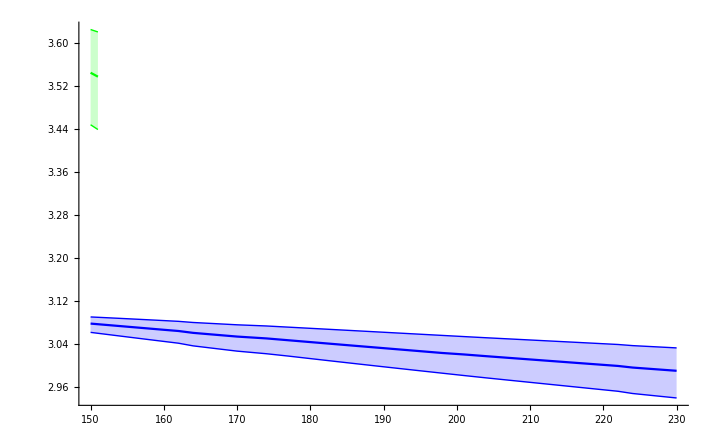

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],wrfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],wrfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],wrfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

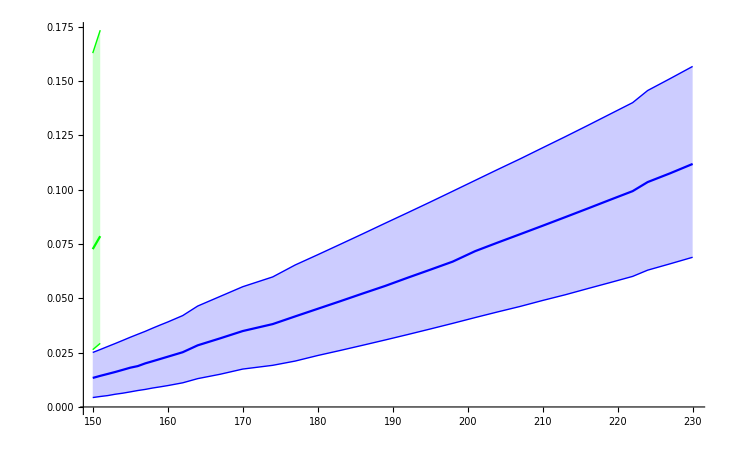

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],Γfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],Γfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],Γfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],Γfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],Γfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],Γfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

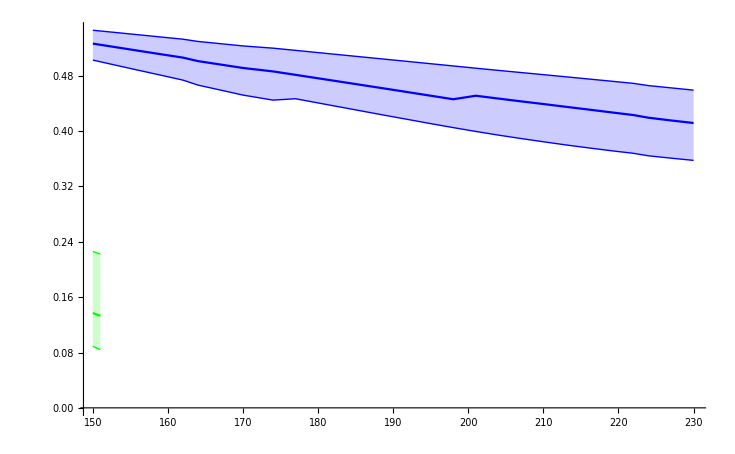

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],areafitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],areafitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],areafitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

### Emission Rates

```mathematica
Emfactor=2.356447552594432;
nB[w_,T_]:=1/(Exp[w/T]-1);
```

```mathematica
R0=ConstantArray[0,ccTcut];
Do[R0[[ii]]={Tscanc[[ii]],Emfactor (areafitcc[[ii,2]]nB[wrfitcc[[ii,2]],Tscanc[[ii]]/1000])/(areafitcc[[ii,1]]nB[wrfitcc[[ii,1]],Tscanc[[ii]]/1000])},{ii,ccTcut}];
```

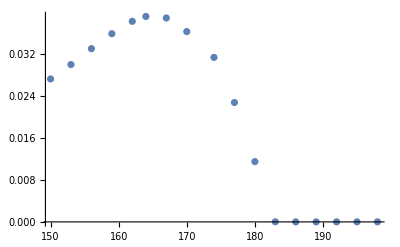

```mathematica
ListPlot[R0]
```

## Bottomonium

```mathematica
Tscanb=IntegerPart[1000 Table[i,{i,0.15,0.6,0.005}]]
```

{150,155,160,164,169,175,180,185,190,195,200,205,210,215,220,224,229,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,329,334,339,345,350,355,360,365,370,375,380,385,390,395,400,405,410,415,420,425,430,435,439,444,449,454,459,464,470,475,480,485,490,495,500,505,510,515,520,525,530,535,540,545,550,555,560,565,570,575,580,585,590,595,600}

```mathematica
Do[bbdata[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"spectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdata[n],Joined->True],{n,1,Length[Tscanb],1}]
```

```mathematica
Do[bbdatal[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"lspectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdatal[n],Joined->True],{n,1,Length[Tscanb],1}]
```

```mathematica
Do[bbdatau[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"uspectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdatau[n],Joined->True],{n,1,Length[Tscanb],1}]
```

### Fitting

```mathematica
fit[bbdata,bbmodel,Tscanb];
fit[bbdatau,bbmodelu,Tscanb];
fit[bbdatal,bbmodell,Tscanb];
```

### Store Results

```mathematica
Do[If[Length[bbmodel[[i]]]>4,bbmodel[[i]]=bbmodel[[i,;;4]]];If[Length[bbmodelu[[i]]]>4,bbmodelu[[i]]=bbmodelu[[i,;;4]]];If[Length[bbmodell[[i]]]>4,bbmodell[[i]]=bbmodell[[i,;;4]]];
If[Length[bbmodel[[i]]]>1,bb1Tcut=i];
If[Length[bbmodelu[[i]]]>1,bb1uTcut=i];
If[Length[bbmodell[[i]]]>1,bb1lTcut=i];
If[Length[bbmodel[[i]]]>2,bb2Tcut=i];
If[Length[bbmodelu[[i]]]>2,bb2uTcut=i];
If[Length[bbmodell[[i]]]>2,bb2lTcut=i];
If[Length[bbmodel[[i]]]>3,bb3Tcut=i];If[Length[bbmodelu[[i]]]>3,bb3uTcut=i,bb3uTcut=1];If[Length[bbmodell[[i]]]>3,bb3lTcut=i];,{i,Length[bbmodel]}];
```

```mathematica
wrfitbb=Range[Length[bbmodel]];
Do[wrfitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[wrfitbb[[i,ii]]=wr/.bbmodel[[i,ii]]["BestFitParameters"],{ii,Length[wrfitbb[[i]]]}],{i,Length[wrfitbb]}]

wrfitbbu=Range[Length[bbmodelu]];
Do[wrfitbbu[[i]]=Range[Length[bbmodelu[[i]]]],{i,Length[bbmodelu]}];
Do[Do[wrfitbbu[[i,ii]]=wr/.bbmodelu[[i,ii]]["BestFitParameters"],{ii,Length[wrfitbbu[[i]]]}],{i,Length[wrfitbbu]}]

wrfitbbl=Range[Length[bbmodell]];
Do[wrfitbbl[[i]]=Range[Length[bbmodell[[i]]]],{i,Length[bbmodell]}];
Do[Do[wrfitbbl[[i,ii]]=wr/.bbmodell[[i,ii]]["BestFitParameters"],{ii,Length[wrfitbbl[[i]]]}],{i,Length[wrfitbbl]}]

Γfitbb=Range[Length[bbmodel]];
Do[Γfitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[Γfitbb[[i,ii]]=Γ/.bbmodel[[i,ii]]["BestFitParameters"],{ii,Length[Γfitbb[[i]]]}],{i,Length[Γfitbb]}]

Γfitbbu=Range[Length[bbmodelu]];
Do[Γfitbbu[[i]]=Range[Length[bbmodelu[[i]]]],{i,Length[bbmodelu]}];
Do[Do[Γfitbbu[[i,ii]]=Γ/.bbmodelu[[i,ii]]["BestFitParameters"],{ii,Length[Γfitbbu[[i]]]}],{i,Length[Γfitbbu]}]

Γfitbbl=Range[Length[bbmodell]];
Do[Γfitbbl[[i]]=Range[Length[bbmodell[[i]]]],{i,Length[bbmodell]}];
Do[Do[Γfitbbl[[i,ii]]=Γ/.bbmodell[[i,ii]]["BestFitParameters"],{ii,Length[Γfitbbl[[i]]]}],{i,Length[Γfitbbl]}]

constfitbb=Range[Length[bbmodel]];
Do[constfitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[constfitbb[[i,ii]]=const/.bbmodel[[i,ii]]["BestFitParameters"],{ii,Length[constfitbb[[i]]]}],{i,Length[constfitbb]}]

constfitbbu=Range[Length[bbmodelu]];
Do[constfitbbu[[i]]=Range[Length[bbmodelu[[i]]]],{i,Length[bbmodelu]}];
Do[Do[constfitbbu[[i,ii]]=const/.bbmodelu[[i,ii]]["BestFitParameters"],{ii,Length[constfitbbu[[i]]]}],{i,Length[constfitbbu]}]

constfitbbl=Range[Length[bbmodell]];
Do[constfitbbl[[i]]=Range[Length[bbmodell[[i]]]],{i,Length[bbmodell]}];
Do[Do[constfitbbl[[i,ii]]=const/.bbmodell[[i,ii]]["BestFitParameters"],{ii,Length[constfitbbl[[i]]]}],{i,Length[constfitbbl]}]

areafitbb=Range[Length[bbmodel]];
Do[areafitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[areafitbb[[i,ii]]=π/2 constfitbb[[i,ii]] Γfitbb[[i,ii]],{ii,Length[areafitbb[[i]]]}],{i,Length[areafitbb]}]

areafitbbu=Range[Length[bbmodelu]];
Do[areafitbbu[[i]]=Range[Length[bbmodelu[[i]]]],{i,Length[bbmodelu]}];
Do[Do[areafitbbu[[i,ii]]=π/2 constfitbbu[[i,ii]] Γfitbbu[[i,ii]],{ii,Length[areafitbbu[[i]]]}],{i,Length[areafitbbu]}]

areafitbbl=Range[Length[bbmodell]];
Do[areafitbbl[[i]]=Range[Length[bbmodell[[i]]]],{i,Length[bbmodell]}];
Do[Do[areafitbbl[[i,ii]]=π/2 constfitbbl[[i,ii]] Γfitbbl[[i,ii]],{ii,Length[areafitbbl[[i]]]}],{i,Length[areafitbbl]}]
```

```mathematica
Manipulate[Show[{ListPlot[bbdatal[i],Joined->True],Plot[bbmodell[[i,ii]][x],{x,0.7 wr/.bbmodell[[i,ii]]["BestFitParameters"],1.3 wr/.bbmodell[[i,ii]]["BestFitParameters"]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wr/.bbmodell[[i,ii]]["BestFitParameters"],Γ/.bbmodell[[i,ii]]["BestFitParameters"],const/.bbmodell[[i,ii]]["BestFitParameters"]],{x,0.7 wr/.bbmodell[[i,ii]]["BestFitParameters"],1.3 wr/.bbmodell[[i,ii]]["BestFitParameters"]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[bbmodel],1},{ii,1,Length[bbmodell[[1]]],1}]
```

```mathematica
bbcont={10.47459661653534,10.386991291819312,10.320189935556595,10.266520483724824,10.221771783701307,10.183415247448838,10.14982884042086,10.119917801704643,10.092912804537864,10.068255145767312,10.045527844650223,10.024869142170065,10.00606442137611,9.988248930352256,9.971300912748175,9.955119189686751,9.939618860084348,9.924728047184722,9.91038541425775,9.896538234463003,9.883140878360269,9.870153615237932,9.857541654132588,9.84527436973816,9.833324672428462,9.821668491664653,9.810284349405235,9.799153005449387,9.788257160460661,9.777581207953114,9.76711102016143,9.756833770672042,9.746737782242517,9.736812392434949,9.727047840979282,9.717435173901784,9.7079661552598,9.698633193697498,9.68942927922979,9.680347923072885,9.67138310961781,9.662529251650565,9.653781149410847,9.645133958371117,9.636583155264336,9.628124512339577,9.61975407153492,9.611468121959486,9.603263180915544,9.595135974071855,9.587083421208572,9.579102619219741,9.571190830899964,9.563345470697755,9.555564095574915,9.547844393123798,9.540184174031799,9.53258136207098,9.525033987912632,9.517540180573716,9.510098162358636,9.502706241507756,9.495362807980896,9.488066327240787,9.48081533651431,9.473608439770503,9.466444304106242,9.459321655963414,9.452239277450436,9.445196003567682,9.438190718761756,9.431222354618207,9.424289886819881,9.41739233320969,9.41052875109574,9.403698235563585,9.396899917176915,9.390132960386843,9.38339656168247,9.376689947990425,9.370012375266969,9.36336312688355,9.35674151254152,9.350146866770242,9.343578547940272,9.33703593705241,9.330518436688472,9.324025470075904,9.317556480121242,9.311110928532827,9.30468829499006};
```

```mathematica
bbbind=bbcont-wrfitbb;
bbbindu=bbcont-wrfitbbu;
bbbindl=bbcont-wrfitbbl;
```

```mathematica
Do[If[(bbbind-Γfitbb)[[i,1]]>0,bb1Tmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbind-Γfitbb)[[i,2]]>0,bb2Tmelt=i],{i,1,bb1Tcut}];
Do[If[(bbbind-Γfitbb)[[i,3]]>0,bb3Tmelt=i],{i,1,bb2Tcut}];
Do[If[(bbbind-Γfitbb)[[i,4]]>0,bb4Tmelt=i],{i,1,bb3Tcut}];
```

```mathematica
Do[If[(bbbindu-Γfitbbu)[[i,1]]>0,bb1uTmelt=i+1],{i,1,Length[bbbind]}];
Do[If[(bbbindu-Γfitbbu)[[i,2]]>0,bb2uTmelt=i+1],{i,1,bb1uTcut}];
Do[If[(bbbindu-Γfitbbu)[[i,3]]>0,bb3uTmelt=i+1],{i,1,bb2uTcut}];
Do[If[(bbbindu-Γfitbbu)[[i,4]]>0,bb4uTmelt=i+1],{i,1,bb3uTcut}];
```

Part::partw: Part 4 of {1.0181,0.464609,0.179054} does not exist.

```mathematica
Do[If[(bbbindl-Γfitbbl)[[i,1]]>0,bb1lTmelt=i+1],{i,1,Length[bbbind]}];
Do[If[(bbbindl-Γfitbbl)[[i,2]]>0,bb2lTmelt=i+1],{i,1,bb1lTcut}];
Do[If[(bbbindl-Γfitbbl)[[i,3]]>0,bb3lTmelt=i+1],{i,1,bb2lTcut}];
Do[If[(bbbindl-Γfitbbl)[[i,4]]>0,bb4lTmelt=i+1],{i,1,bb3lTcut}];
```

Part::partw: Part 2 of {0.341225} does not exist.

Part::partw: Part 3 of {0.131692,-0.168538} does not exist.

Part::partw: Part 3 of {0.0251157,-0.27029} does not exist.

```mathematica
N[{Tscanb[[bb1lTmelt]],Tscanb[[bb1Tmelt]],Tscanb[[bb1uTmelt]]}/155]
```

{3.03226,3.03226,3.12903}

```mathematica
N[{Tscanb[[bb2lTmelt]],Tscanb[[bb2Tmelt]],Tscanb[[bb2uTmelt]]}/155]
```

{1.35484,1.32258,1.3871}

```mathematica
N[{Tscanb[[bb3lTmelt]],Tscanb[[bb3Tmelt]],Tscanb[[bb3uTmelt]]}/155]
```

{1.,1.03226,1.05806}

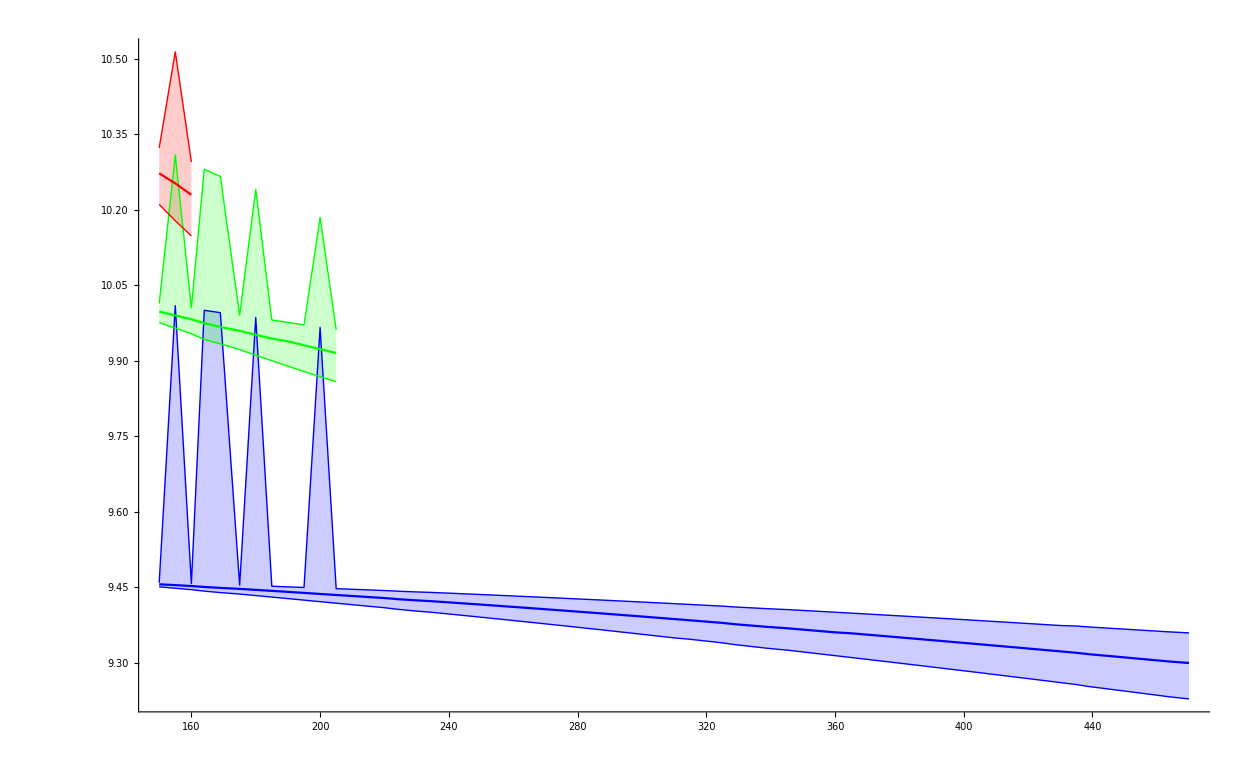

```mathematica
ListPlot[{Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

```mathematica
n=2;
input=bbdatal;
```

```mathematica
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];
maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]]
```

{9.45822,9.45822,10.0097,10.0099,10.3096,10.5166,10.6651}

```mathematica
If[maxxs[[2]]/maxxs[[1]]≤1.001,maxxs=Delete[maxxs,2]]
```

```mathematica
maxxs
```

{9.45822,10.0097,10.3096,10.5166,10.6651}

```mathematica
maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]]
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}]
```

{712,1277,1584,1796,1948}

{96.4663,5.2427,1.18633,0.409938,0.21514}

```mathematica
bad={};
Do[If[maxys[[i]]<maxys[[i+1]],bad=Append[bad,i]],{i,Length[maxys]-1}]
Do[maxxs=Delete[maxxs,bad[[i]]];maxys=Delete[maxys,bad[[i]]];maxxis=Delete[maxxis,bad[[i]]];,{i,Length[bad]}]
```

```mathematica
bad
```

{}

```mathematica
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];
mins=Append[Prepend[mins,maxxis[[1]]-2 (mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),maxyi+3(maxyi-hwhmi)};]
```

```mathematica
If[mins[[1]]≤0,mins[[1]]=1];
```

```mathematica
mins
```

{182,977,1425,1688,1872,2024}

```mathematica
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
```

```mathematica
hwhmi
```

{711,1272,1570,1765,1872}

```mathematica
Do[If[Or[2 input[n][[hwhmi[[-i]],2]]≤0.5 maxys[[-i]],2 input[n][[hwhmi[[-i]],2]]≥1.5 maxys[[-i]]],hwhmi[[-i]]=maxxis[[-i]]],{i,Length[hwhmi]-1}]
```

```mathematica
hwhmi
```

{711,1272,1570,1765,1872}

```mathematica
bad=Position[maxxis-hwhmi,0]
```

{}

```mathematica
hwhmi=DeleteCases[maxxis-hwhmi,0]
```

{1,5,14,31,76}

```mathematica
maxxis=Delete[maxxis,bad];
maxxs=Delete[maxxs,bad];
maxys=Delete[maxys,bad];
```

```mathematica
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];
mins=Append[Prepend[mins,maxxis[[1]]-2 (mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),maxyi+3(maxyi-hwhmi)};
hwhmi={hwhmi};];
```

```mathematica
mins
```

{182,977,1425,1688,1872,2024}

```mathematica
If[mins[[1]]≤0,mins[[1]]=1];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
hwhmi=DeleteCases[maxxis-hwhmi,0];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[maxxis[[i]]-hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[mins[[i]];;mins[[i+1]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w],{i,Length[hwhmi]}];
```

Set::pkspec1: The expression ii cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.